# Tonello 1 (4,5,3,2)

by  F. Avram and R. Adenane and AD. Halanay

β, α matrices (for Matlab) are

[1 1 1 1 0; 0 0 0 0 1; 1 0 0 0 0; 0 1 0 0 0]

[1 1 0 0 1; 1 1 0 0 0; 0 0 1 0 0; 0 0 0 1 0]

RN= {A+B→A+C,A+B→A+D,C→A,D→A,A→B}

Tonello 1(0 | 0 | 1 | 1 | -1
-1 | -1 | 0 | 0 | 1
1 | 0 | -1 | 0 | 0
0 | 1 | 0 | -1 | 0) has rank 3  deficiency δ=N-L-S=7-2-3=2 cons {A+B+C+D} fluxes(k_1+k_3+k_5
k_2+k_4+k_5) RHS (C k_3+D k_4-A k_5
-A (B k_1+B k_2-k_5)
A B k_1-C k_3
A B k_2-D k_4)

4 variables={c_A,c_B,c_C,c_D}={A,B,C,D}

The FHJ graph by Reaction Kinetics and by EpidCRN are

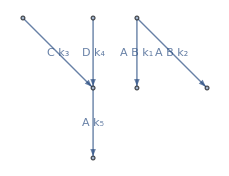

groups

-Graphics-

Solve::svars: Equations may not give solutions for all "solve" variables.

Fixed points are {{A→0,C→0,D→0},{B→k_5/(k_1+k_2),C→(A k_1 k_5)/((k_1+k_2) k_3),D→(A k_2 k_5)/((k_1+k_2) k_4)}}

```mathematica
ClearAll["Global‘*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession, NotebookAutoSave -> True];
NotebookSave[];AppendTo[$Path,"C:\\Users\\flori\\Dropbox\\Codes"];<<EpidCRN`;(*Names["EpidCRN`*"]*)
Needs["ReactionKinetics`"];
Format[γr]:=Subscript[γ,r];Format[βr]:=Subscript[β,r];Format[μi]:=Subscript[μ,i];Format[γs]:=Subscript[γ,s];
Format[nt]:=Subscript[n,tot];
Format[k1]:=Subscript[k,1];Format[k2]:=Subscript[k,2];
Format[k3]:=Subscript[k,3];Format[k4]:=Subscript[k,4];Format[k5]:=Subscript[k,5];
Format[k6]:=Subscript[k,6];
Format[k7]:=Subscript[k,7];Format[k8]:=Subscript[k,8];Format[k9]:=Subscript[k,9];
cDFE={X->0,Xt->0,Y->0,Xp->xT,Yp->yT};
(* RN is a (5,4,3) CRN*)
RN={"A" +"B"-> "A"+"C", "A" +"B"-> "A"+"D", "C" ->"A", "D" ->"A","A" ->"B"};var={A,B,C,D};
RND=ReactionsData[RN];
Γ= RND["γ"]//Normal;
expo= RND["α"]//Normal//Transpose;
prod=RND["β"]//Normal//Transpose;
Print["β, α matrices (for Matlab) are "]
mat2Matl[prod//Transpose]
mat2Matl[expo//Transpose]

Print["RN= ", RN]
{comp,reac,nR,spec,nS,vol,vars,defi}=RND["complexes","reactionsteps","R","species","M","volpertgraph",
"variables","deficiency"];
con=cons[Γ];conx=con.var;
tk=Array[Symbol["k" <> ToString[#]] &, nR];cp=Thread[tk>0];cv=Thread[var>=0];
 ct=Join[cp,cv];rk=Array[Symbol["k" <> ToString[#]] &, nR];
rv=expM[var,expo];
Rv=tk*rv;
RHS=Γ.Rv//Factor;
fl=(cons[Γ//Transpose]).rk;

Print["Tonello 1",Γ//MatrixForm, " has rank ",MatrixRank[Γ],
"  deficiency ", RND["deficiency"]," cons ",conx,
" fluxes",fl//MatrixForm," RHS ",RHS//MatrixForm]
Print[RND["variables"]//Length," variables=",RND["variables"],"=",var]

Print["The FHJ graph by Reaction Kinetics and by EpidCRN are"]
ShowFHJGraph[RN,Rv,DirectedEdges->True,VertexLabeling->True,ImageSize->230]
Print["groups"]
groups = {{"B","D","C","A"}};

FHJ[comp, RN, Rv,.60, groups]
fp=Solve[(RHS)==0, var]//FullSimplify;
Print["Fixed points are ", fp]
```

#### Computation of R0 using NGM script:

```mathematica
(*NGM  cell*)
jac=Grad[RHS,var];
mod={RHS,var,tk};

inf={1,3,4};  
jI=Grad[RHS[[inf]],var[[inf]]];
ng=NGM[mod,inf];jI=ng[[1]];K=ng[[6]];
Print["The Jacobian of infectious equations:", RHS[[inf]]//MatrixForm, " has jI= ",jI//MatrixForm];
F=ng[[4]]/.cDFE;Tm=ng[[5]]/.cDFE;
Print["F= ",F//MatrixForm,"-V= ",Tm//MatrixForm];
Print["K=",K//MatrixForm," has rank ",K//MatrixRank," and eig"]
eig=K//Eigenvalues
Print["chp of jI="]
chJ=CharacteristicPolynomial[ng[[1]],u]//Factor
Print["chp of K="]
chK=CharacteristicPolynomial[ng[[6]],u]//Factor
Print["chp of K after substituting u->x+1"]
px=chK/.u->x+1//Factor
```

The Jacobian of infectious equations:(C k_3+D k_4-A k_5
A B k_1-C k_3
A B k_2-D k_4) has jI= (-k_5 | k_3 | k_4
B k_1 | -k_3 | 0
B k_2 | 0 | -k_4)

F= (0 | 0 | 0
B k_1 | 0 | 0
B k_2 | 0 | 0)-V= (-k_5 | k_3 | k_4
0 | -k_3 | 0
0 | 0 | -k_4)

K=(0 | 0 | 0
(B k_1)/k_5 | (B k_1)/k_5 | (B k_1)/k_5
(B k_2)/k_5 | (B k_2)/k_5 | (B k_2)/k_5) has rank 1 and eig

{0,0,(B (k_1+k_2))/k_5}

chp of jI=

B k_1 k_3 k_4+B k_2 k_3 k_4-k_3 k_4 k_5+B k_1 k_3 u+B k_2 k_4 u-k_3 k_4 u-k_3 k_5 u-k_4 k_5 u-k_3 u^2-k_4 u^2-k_5 u^2-u^3

chp of K=

(u^2 (B k_1+B k_2-k_5 u))/k_5

chp of K after substituting u->x+1

-((1+x)^2 (-B k_1-B k_2+k_5+k_5 x))/k_5

```mathematica
(*Jacobian at EE; there is no Hopf*)

jaE=Grad[RHS,var]//.fp[[2]];
Print["jaE at EE is",jaE//MatrixForm]
Print["ChP is "]
ch=(CharacteristicPolynomial[jaE,λ]//Factor)/(λ)//Factor
Print["with positive coefficients"]
co=CoefficientList[ch,λ]//FullSimplify

Print["Eigenvalues for jac(EE)"]
eig=Eigenvalues[jaE]//FullSimplify
```

jaE at EE is(-k_5 | 0 | k_3 | k_4
k_5-(k_1 k_5)/(k_1+k_2)-(k_2 k_5)/(k_1+k_2) | -A (k_1+k_2) | 0 | 0
(k_1 k_5)/(k_1+k_2) | A k_1 | -k_3 | 0
(k_2 k_5)/(k_1+k_2) | A k_2 | 0 | -k_4)

ChP is

1/(k_1+k_2)(A k_1+A k_2+λ) (k_1 k_3 k_4+k_2 k_3 k_4+k_2 k_3 k_5+k_1 k_4 k_5+k_1 k_3 λ+k_2 k_3 λ+k_1 k_4 λ+k_2 k_4 λ+k_1 k_5 λ+k_2 k_5 λ+k_1 λ^2+k_2 λ^2)

with positive coefficients

{A (k_1 k_4 (k_3+k_5)+k_2 k_3 (k_4+k_5)),(k_1 k_4 (k_3+k_5)+k_2 k_3 (k_4+k_5)+A (k_1+k_2)^2 (k_3+k_4+k_5))/(k_1+k_2),A (k_1+k_2)+k_3+k_4+k_5,1}

Eigenvalues for jac(EE)

{0,-A (k_1+k_2),-((k_1+k_2) (k_3+k_4+k_5)+√((k_1+k_2) (k_1 (k_3-k_4+k_5)^2+k_2 (-k_3+k_4+k_5)^2)))/(2 (k_1+k_2)),(-((k_1+k_2) (k_3+k_4+k_5))+√((k_1+k_2) (k_1 (k_3-k_4+k_5)^2+k_2 (-k_3+k_4+k_5)^2)))/(2 (k_1+k_2))}

### Translated SIRS model (WR/DZ case):

Tonello 1(0 | 0 | 1 | 1 | -1
-1 | -1 | 0 | 0 | 1
1 | 0 | -1 | 0 | 0
0 | 1 | 0 | -1 | 0) has rank 3  deficiency δ=N-L-S=4-1-3=0 cons {A+B+C+D} fluxes(1 | 0
0 | 1
1 | 0
0 | 1
1 | 1) RHS (C k_3+D k_4-A k_5
-A (B k_1+B k_2-k_5)
A B k_1-C k_3
A B k_2-D k_4)

4 variables={c_A,c_B,c_C,c_D}={A,B,C,D}

The FHJ graph

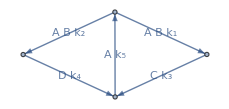

{{A+B,A+C,A+D,2 A}}

-Graphics-

{{A→0,B→n_tot,C→0,D→0},{A→(k_3 k_4 (-k_5+(k_1+k_2) n_tot))/(k_1 k_4 (k_3+k_5)+k_2 k_3 (k_4+k_5)),B→k_5/(k_1+k_2),C→(k_1 k_4 k_5 (-k_5+(k_1+k_2) n_tot))/((k_1+k_2) (k_1 k_4 (k_3+k_5)+k_2 k_3 (k_4+k_5))),D→(k_2 k_3 k_5 (-k_5+(k_1+k_2) n_tot))/((k_1+k_2) (k_1 k_4 (k_3+k_5)+k_2 k_3 (k_4+k_5)))}}

Check rap{0,0,0,0} sum is n_tot

n_tot∈ℝ&&B>n_tot

```mathematica
RNt={"A" +"B"-> "A"+"C", "A" +"B"-> "A"+"D", "A"+"C" ->2"A", "A"+"D" ->2"A",2"A" ->"A"+"B"};
 
 RND=ReactionsData[RNt];
Γ= RND["γ"]//Normal;
expo= RND["α"]//Normal//Transpose;
{comp,reac,nR,spec,nS,vol,vars,defi}=RND["complexes","reactionsteps","R","species","M","volpertgraph",
"variables","deficiency"];
con=cons[Γ];conx=con.var;
tk=Array[Symbol["k" <> ToString[#]] &, nR];cp=Thread[tk>0];cv=Thread[var>=0];
 ct=Join[cp,cv];

RHS=Γ.Rv//Factor;
fl=cons[Γ//Transpose]//Transpose;

Print["Tonello 1",Γ//MatrixForm, " has rank ",MatrixRank[Γ],
"  deficiency ", RND["deficiency"]," cons ",conx,
" fluxes",fl//MatrixForm," RHS ",RHS//MatrixForm]
Print[RND["variables"]//Length," variables=",RND["variables"],"=",var]

Print["The FHJ graph"]
ShowFHJGraph[RNt,Rv,DirectedEdges->True,VertexLabeling->True,ImageSize->230]
groups = {{comp[[1]],comp[[2]],comp[[3]],comp[[4]]}}

FHJ[comp, RNt, Rv,.60, groups]

fp=Solve[Append[Thread[RHS==0],Total[var]==nt],var]//FullSimplify
Print["Check rap",RHS/.fp[[2]]//FullSimplify," sum is ",to=Total[var]/.fp[[2]]//FullSimplify]
Assuming[ct,Reduce[to<B]//Refine]
```